## Background

### Problem Statement

I have a GPX Track file, such as might be created when planning a bicycle route on ridewithgps.com. This file consists of a sequence of GPS coordinates as “track points” defining the course I plan to take, and also a set of “waypoints”, which are the coordinates of points of interest along the way, such as water refill stations, scenic views, or so on. Note that GPX waypoints may not necessarily be located directly on the course.

For each waypoint, I’d like to compute how far along it is on the total course, assuming it’s positioned reasonably nearby. This information would let me re-export the waypoints on the course as “course points” in a Garmin FIT file, which must specify a distance from the start of the course. This file can then be used on a Garmin Edge bicycle computer, which will display a handy list of upcoming course points with the distance and estimated time remaining to each:

-Graphics-

To do this, I need to solve the following problem: Given a geodesic representing a segment of a track and a separate point, (1) what is the minimum distance between the point and the geodesic segment, and (2) at what distance along the segment is its closest distance to the separate point obtained? This is sometimes called the “interception problem”, in the sense of an anti-aircraft battery finding the nearest point of intercept for an aircraft flying near it. (N.B.: To my knowledge, none of my Ride with GPS POIs are armed with missiles.)

There are a few possible methods of computing this answer. The purpose of this notebook is to quantify the deviation that can be expected from the “real” geodesic solution when applying these approximations, at the scales I’m likely to encounter.

### Earth Model

I’m using the WGS84 ellipsoid model of the Earth, which is the standard for GPS. I won’t apply any additional geoid data for elevation corrections in my distance calculations.

See Karney’s 2011 paper, Geodesics on an ellipsoid of revolution, for a great introduction to geodesic calculations.

## Relevant Scales of Distance

To start with, it’d be good to know what sort of distances we’re dealing with.

### Track Segment Scale

We can get a distribution of track segment (i.e., the geodesic segments between consecutive track points) lengths by examining a route exported from RideWithGPS. Here, for an example, is RAGBRAI 2024's Day 4 gravel route, exported as a GPX Track:

```mathematica
importRelative[filename_,args___]:=Import[If[$CloudEvaluation,CloudObject[filename],FileNameJoin[{NotebookDirectory[],"sample-files",filename}]],args]
```

```mathematica
gpxFilename="RAGBRAI__Day_4_Gravel_Option.gpx.gz";
importRelative[gpxFilename,"Graphics"]
```

-Graphics-

The route is comprised of thousands of track points:

```mathematica
gpxTrackLine=importRelative[gpxFilename,"Data"][[1]]//Association//Lookup[#,"Geometry"]&//Part[#,1,1,1]&
```

GeoPosition[…]

Which have a distribution of their individual lengths :

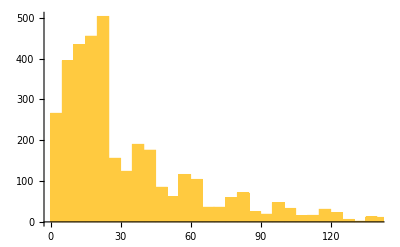

```mathematica
trackSegmentLengths=UnitConvert[GeoDistance@@@Partition[gpxTrackLine[[1]],2,1],"Meters"];Histogram[trackSegmentLengths]
```

```mathematica
With[{descriptions={Length,Mean,Median,Max,Total}},
Grid[{descriptions,#[trackSegmentLengths]&/@descriptions},Frame->All]]
```

Length | Mean | Median | Max | Total
3589 | 35.9035 m | 20.1299 m | 481.124 m | 128857. m

So we can presume most geodesic segments we’re dealing with are quite short, on the order of tens of meters; but that others may be closer to 500m. The total route distance may reach the hundreds of kilometers on routes like this, or even longer for ultra-endurance rides like RAAM.

Note that many segments may have zero length:

```mathematica
Length[Select[trackSegmentLengths,#==Quantity[0,"Meters"]&]]
```

47

### Track Point Precision

In GPX Track files exported by RideWithGPS, the latitude and longitude of track points have five decimal places of precision. (Meanwhile, waypoints have up to 14 decimal places.) What precision of track point position does this correspond to?

The length of an arcminute of longitude is at its greatest along the equator. There, we see a precision of five decimal places corresponds to a geodesic distance of:

```mathematica
showPrecision[lat_,pointsFn_]:=
With[{deltas={{"5 decimals",10^-5},{"13 decimals",10^-13},{"14 decimals",10^-14},{"semicircle",180/2^31}}},
Grid[{#[[1]]&/@deltas,UnitConvert[#,"Meters"]&/@GeoDistance/@(((pointsFn[lat,#]&)/@(#[[2]]&))/@deltas)},Frame->All]]
```

```mathematica
showPrecision[0.0, Function[{lat,delta},{{lat, 0.0},{lat,delta}}]]
```

5 decimals | 13 decimals | 14 decimals | semicircle
1.11319 m | 1.11319×10^-8 m | 0. m | 0.00933069 m

Meanwhile, the longest arcminute of latitude is near the poles. There:

```mathematica
showPrecision[90.0, Function[{lat,delta},{{lat-delta, 0.0},{lat,0.0}}]]
```

5 decimals | 13 decimals | 14 decimals | semicircle
1.11694 m | 1.13298×10^-8 m | 0. m | 0.00936208 m

(A “semicircle” refers to Garmin’s 32-bit integer representation of latitude and longitude as encoded in FIT files.)

To accommodate for this imprecision in exported GPX tracks, we’ll want to use a threshold point-to-geodesic distance on the order of at least tens of meters.

## Point-to-Point Distances

The problem of computing the length and azimuth of a geodesic between two points on the ellipsoid is known as the “inverse problem”, and there are widely-available implementations such as in Karney’s geographiclib that, while iterative, are quite efficient. This means it isn’t necessary to apply a linear approximation in order to simply find the distance between two points.

However, knowing at what scale this approximation breaks down can provide some intuition about solving the interception problem, where a linear approximation might be more helpful.

### Linear Approximation Using 3D Cartesian Coordinates

For relatively close-together points, such as track points along a single-day cycling route, what’s the discrepancy between the length of a geodesic path and the 3D line segment (i.e., chord) between them? This is illustrated in exaggerated form below.

```mathematica
With[{semiMajor=5,semiMinor=3,lf=1.1},Show[With[{p1={0,0,semiMinor},p2={semiMajor,0,0}},Graphics3D[{PointSize[Large],Blue,Point[p1],Red,Point[p2],Thick,Line[{p1,p2}],Black,Text["p",lf*{semiMajor,0,0}],Text["target point",lf*{0,0,semiMinor}],Text["distance chord",lf*(2p1+3p2)/5],Text["distance geodesic",lf*{semiMajor/Sqrt[2],0,semiMinor/Sqrt[2]}],Opacity[0.7],LightGreen,Ellipsoid[{0,0,0},{semiMajor,semiMajor,semiMinor}]}]],ParametricPlot3D[{semiMajor*Cos[u],0,semiMinor*Sin[u]},{u,0,Pi/2},PlotStyle->Red],ViewPoint->{Pi/2,-3Pi/4,Pi/4},ViewVertical->{0,0,1}]]
```

-Graphics3D-

```mathematica
(* Find the chord distance between two GeoPositions on the ellipsoid. *)
chordDistance[a_,b_]:= Norm[List @@ GeoPositionXYZ[a] - List @@ GeoPositionXYZ[b]]

(* Randomly choose a start position and azimuth on the reference ellipsoid,and return the chord distance between start and end corresponding to the given geodesic length. *)
randomChordDistance[geodesicDistance_]:=With[{startPos=RandomGeoPosition[],azimuth=RandomReal[360-$MachineEpsilon]},chordDistance[startPos,GeoDestination[startPos,{geodesicDistance,azimuth}]]]
```

By plotting chord distance ratio against geodesic distance from random starting points and azimuths, we can see that this approximation decreases significantly from the actual geodesic distance only at scales far larger than we’re concerned with:

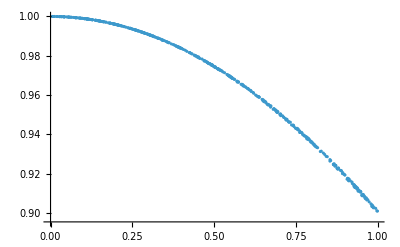

```mathematica
ListPlot[ParallelTable[With[{geodesicDistance=RandomReal[10000000]},With[{chordDistance=randomChordDistance[geodesicDistance]},{geodesicDistance,chordDistance/geodesicDistance}]],500]]
```

We can then generate distributions of errors in the chord approximation (as differences in meters) for random geodesics at varying orders of magnitude:

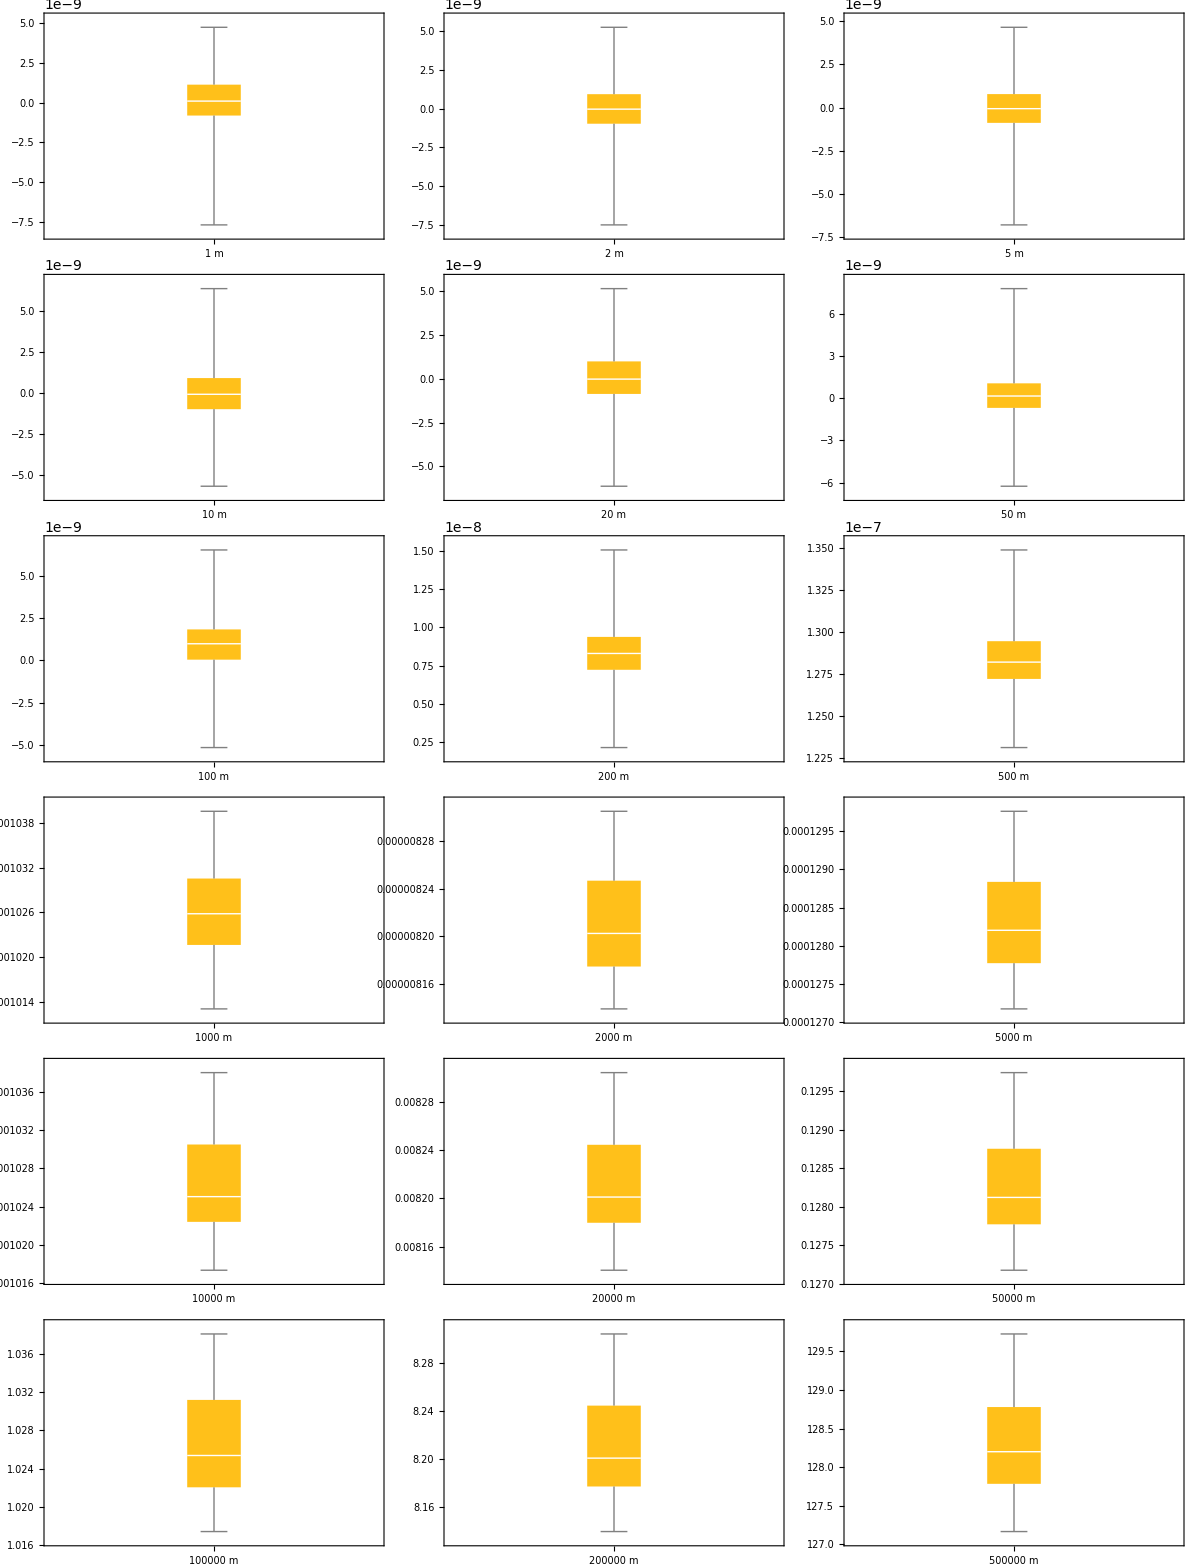

```mathematica
With[{geodesicDistances={#,2#,5#}&/@(10^Range[0,5]),n=300},Grid[ParallelMap[Function[d,BoxWhiskerChart[Table[randomChordDistance[d]//(d-#)&,n],ChartLabels->{Quantity[d,"Meters"]}]],geodesicDistances,{2}]]]
```

So for example, we can see that the median error due to the chord approximation is around 1mm at distances of around 10km, 1m at 100km, and 128m at 500km.

At distances of 100m and lower, the errors are on the scale of nanometers and can be either positive or negative. At this scale, those errors may be dominated by limits of numerical precision.

This means that for most track segments we’ll see in practice, using a Cartesian approximation of the distance between the segment and a third point is very reasonable!

### Why Not an Equirectangular Projection?

One question I’ve been asked is why not simply use an equirectangular projection—essentially treating the longitude and latitude as X and Y coordinates?

```mathematica
GeoGraphics[GeoRange->"World",GeoProjection->"Equirectangular",Frame->True]
```

-Graphics-

One issue is that the length of an arcminute of latitude or longitude varies as we move from the equator to the poles, and that of an arcminute of longitude varies significantly enough that we’d have to compensate for it:

```mathematica
latArcMinute[lat_]:=UnitConvert[GeoDistance[{lat,0},{lat+1/60,0}],"Meters"]
lonArcMinute[lat_]:=UnitConvert[GeoDistance[{lat,0},{lat,1/60}],"Meters"]
```

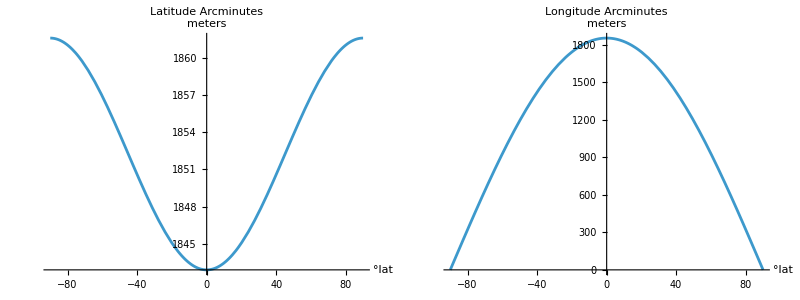

```mathematica
Grid[{{Plot[latArcMinute[lat],{lat,-90,90-1/60},PlotLabel->"Latitude Arcminutes",AxesLabel->{"°lat","meters"}],Plot[lonArcMinute[lat],{lat,-90,90},PlotLabel->"Longitude Arcminutes",AxesLabel->{"°lat","meters"}]}}]
```

For example, the length of an arcminute of longitude varies by 53% between Vancouver and Singapore:

```mathematica
With[{placeLatitude=Function[place,GeoPosition[place][[1,1]]]},
lonArcMinute[placeLatitude[Entity["Country","Singapore"]]]/lonArcMinute[placeLatitude[Entity["City",{"Vancouver","BritishColumbia","Canada"}]]]]
```

1.52951

Using an equirectangular projection would also add edge cases around the anti-meridian and the poles (however unlikely it may be for someone to plan a cycling route across the north or south poles!). Using a 3D Cartesian space, in contrast, still reduces the problem to non-iterative linear algebra without adding these incidental sources of complexity.

## Point-to-Geodesic Distances

Now we come to the original problem statement: Given a geodesic representing a segment of a track and a separate point, (1) what is the minimum distance between the point and the geodesic segment, and (2) at what distance along the segment is its closest distance to the separate point obtained?

```mathematica
With[{semiMajor=5,semiMinor=3,lf=1.1},Show[With[{p1={0,-semiMajor/Sqrt[2],semiMinor/Sqrt[2]},p2={0,semiMajor/Sqrt[2],semiMinor/Sqrt[2]},p3={semiMajor,0,0}},Graphics3D[{PointSize[Large],Blue,Point[p1],Point[p2],Thick,Line[{p1,p2}],Red,Point[p3],Line[{p3,(p1+p2)/2}],Black,Text["p",lf*{semiMajor,0,0}],Text["target geodesic",lf*{0,0,semiMinor}],Text["target chord",lf*{0,0,(semiMinor/Sqrt[2])}],Text["distance geodesic",lf*{semiMajor/Sqrt[2],0,semiMinor/Sqrt[2]}],Text["distance line",lf*(p1+p2+2p3)/4],Opacity[0.7],LightGreen,Ellipsoid[{0,0,0},{semiMajor,semiMajor,semiMinor}],Opacity[0.08],Orange,InfinitePlane[{p1,p2,p3}]}]],ParametricPlot3D[{0,semiMajor*Cos[u],semiMinor*Sin[u]},{u,Pi/4,3Pi/4},PlotStyle->Blue],
ParametricPlot3D[{semiMajor*Cos[u],0,semiMinor*Sin[u]},{u,0,Pi/2},PlotStyle->Red],ViewPoint->{Pi/2,-3Pi/4,Pi/4},ViewVertical->{0,0,1}]]
```

-Graphics3D-

Thanks to the appropriately-named user arcseconds on irc.sdf.org, who pointed out that this could be approximated as a problem on a plane intercepting the Earth ellipsoid.

### Minimizing the Inverse Solution

One way to do this is to choose a point on the target geodesic and perform numerical optimization of its position along the target, minimizing the solution of the inverse problem between that point and p. This is inefficient (iteration on top of iteration), but it provides a precise answer:

```mathematica
(* Returns a random geodesic of the given length. *)
randomGeodesic[geoDistance_]:=
With[{startPos=RandomGeoPosition[],azimuth=RandomReal[360-$MachineEpsilon]},
<|"startPos"->startPos,"endPos"->GeoDestination[startPos,{geoDistance,azimuth}],"geoDistance"->geoDistance,"azimuth"->azimuth|>]

(* Given a point p and a geodesic target defined by its start point and its starging azimuth: Finds the distance between p and the geodesic at distance d from its start. *)
pointToGeodesicPointDistance[p_,target_,d_?NumericQ]:=With[{targetPoint=GeoDestination[target[["startPos"]],{d,target[["azimuth"]]}]},QuantityMagnitude[UnitConvert[GeoDistance[p,targetPoint]],"Meters"]]

(* Given a point and a target geodesic, find the minimum distance between the two. *)
pointToGeodesicMin[p_,target_]:=
NMinimize[{pointToGeodesicPointDistance[p,target,d],d>=0&&d<=target[["geoDistance"]]},d]
```

```mathematica
pointToGeodesicMin[RandomGeoPosition[],randomGeodesic[20]]
```

{1.03349×10^7,{d→20.}}

### Linear Approximation

We can compute a linear projection of a point onto a line segment with some simple linear algebra:

```mathematica
pointToSegmentProjection[segmentStart_,segmentEnd_,p_]:=With[{b=segmentEnd-segmentStart,a=p-segmentStart},
segmentStart+
If[Dot[a,b]<=0,{0,0,0},
With[{aProj=b*Dot[a,b]/Dot[b,b]},
If[Dot[aProj,aProj]<Dot[b,b],aProj,b]]]]
```

If the projection onto the line extending through the segment would lie beyond the segment’s endpoints, this calculation returns the nearest segment endpoint instead. So it sort of “sticks” to the target chord even as p moves about:

```mathematica
Manipulate[With[{targetStart={-4,0,0},targetEnd={4,0,0},p={10*Cos[2*t],10*Cos[3*t],10*Cos[5*t]}},With[{bp=pointToSegmentProjection[targetStart,targetEnd,p]},
Graphics3D[{PointSize[Large],Thick,Blue,Point[bp],Line[{targetStart,targetEnd}],Red,Point[p],Line[{p,bp}],Black,Text["p",p+{0,0,1}],Text["target chord",{(targetStart+targetEnd)/2+{0,0,-2}}]},PlotRange->{{-11,11},{-11,11},{-11,11}},ViewPoint->{-12,-5,5}]]],
{t,0,2Pi-$MachineEpsilon}]
```

A variation of the above uses geocentric (XYZ) Cartesian coordinates to quickly estimate the minimum distance between a point on the ellipsoid and a geodesic segment:

```mathematica
pointToGeodesicLinearDistance[pCoords_,target_]:=
With[{targetStart=GeoPositionXYZ[target[["startPos"]]][[1]],targetEnd=GeoPositionXYZ[target[["endPos"]]][[1]],p=GeoPositionXYZ[pCoords][[1]]},
With[{b=targetEnd-targetStart,a=p-targetStart},
Norm[a-If[Dot[a,b]<=0,{0,0,0},
With[{aProj=b*Dot[a,b]/Dot[b,b]},
If[Dot[aProj,aProj]<Dot[b,b],aProj,b]]]]]]
```

The accuracy of this approximation can be estimated by plotting it against the actual geodesic distances between random points and targets:

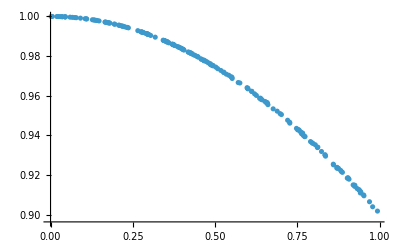

```mathematica
(* Given a geodesic, returns a random point at a specified distance from its midpoint *)
randomPointAroundGeodesic[geodesic_,pointDistance_]:=
With[{midpoint=GeoDestination[geodesic[["startPos"]],{geodesic[["geoDistance"]],geodesic[["azimuth"]]}],azimuth=RandomReal[360-$MachineEpsilon]},
GeoDestination[midpoint,{pointDistance,azimuth}]]

linearDistanceGains=ParallelTable[
With[{target=randomGeodesic[400]},
With[{p=randomPointAroundGeodesic[target,RandomReal[10000000]]},
With[{actualDistance=pointToGeodesicMin[p,target][[1]],linearDistance=pointToGeodesicLinearDistance[p,target]},
{actualDistance,linearDistance/actualDistance}]]],200];

ListPlot[linearDistanceGains]
```

As with the linear estimate of point-to-point distances, we can conclude that this serves as a suitable approximation even at reasonably high distances from the target geodesic. In particular, when attempting to find the nearest course segment to a point, this approximation would be useful for filtering out far-away segments before then applying a more accurate computation to a smaller set of candidates.

### Chord Depth

When using the linear approximation to filter out segments far away from a point, the approximation will generally be shorter than the actual geodesic distance, assuming the target segment is shorter than its distance from the point.

However, a degenerate case occurs if the target segment is very long, and the point is located very close to its midpoint. In this case, the linear approximation will be longer than the actual geodesic distance, because the “target chord” will lie at some non-negligible depth below the surface. So for correctness, when using the linear approximation to filter out far-away course segments, we must consider their maximum possible depth below the surface as a sort of “padding”.

Because WGS84 is a flattened ellipsoid of revolution, the maximum possible depth for any given chord length will occur if the chord is parallel to the ellipse’s minor axis:

```mathematica
(* Ellipsoid parameters copied from GeographicLib.NET *)
wgs84a=6378137.0;
wgs84f=1/298.257223563;
wgs84b=wgs84a*(1-wgs84f);

maxChordDepth[chordLength_]:=wgs84a*(1-√(1-chordLength^2/(4*wgs84b^2)))
```

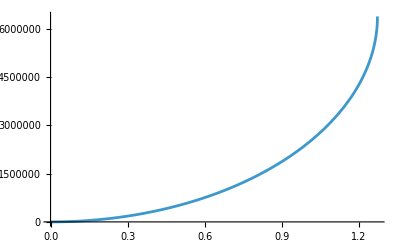

```mathematica
Plot[maxChordDepth[x],{x,0,wgs84b*2}]
```

We can see we’ll reach a maximum theoretical chord depth at a chord length of around 7km:

```mathematica
NMinimize[{(maxChordDepth[x]-1.0)^2,x>0&&x<2*wgs84b},x]
```

{5.02629×10^-22,{x→7119.24}}

When filtering candidate segments with the linear approximation, we can work around this by adding the max chord depth given by the above formula—or to be precise, the hypotenuse of the max chord depth and the intended search radius. Alternately, we could add say 200m to search radii uniformly, rejecting any chords of greater than 100km in length:

```mathematica
NMinimize[{(maxChordDepth[x]-200.0)^2,x>0&&x<2*wgs84b},x]
```

{5.53142×10^-20,{x→100680.}}

### Gnomonic Projection

See Karney’s post about this problem, referenced by the documentation of the Rust icao-wgs84 crate.

In summary, it’s possible to use a variant of the gnomonic projection to solve this problem by choosing a candidate point along the geodesic, using it as the center point for a gnomonic projection, and then solving planar intersection on the projection to find a new candidate point. We can then iterate until the solution converges.

```mathematica
GeoGraphics[{GeoMarker[{45,45}],GeoPath[{{45,-45},{-45,45}},"Geodesic"]},GeoProjection->{"Gnomonic","Centering"->GeoPosition[{0,0}]}]
```

-Graphics-

A limitation of this method is that it only works for points and segments within a radius of around 10000km, but the linear approximation described above makes a good filter pass for this.